```mathematica
ClearAll["Global`*"]
```

Reproductive energetics for a mammalian carnivore

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*)
```

```mathematica
λPred[Mp]
```

-(7.25474×10^-7)/(Mp^(1/4) Log[0.0127415/(1-0.558075/Mp^0.02)])

```mathematica
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
(*E'=2*7000; (*J/g*)
a'=B0/E';*)
(*m[t_,Mp_]:=Mp*E^(-a*t/(Mp^(1-η)));Bpred[Mp_]:=Integrate[B0*m[t,Mp]^(η),{t,0,τLamPred[Mp]}]*)
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator individuals per area seems suspect because intercept should be *much less* than prey individuals per area... right now predator intercept is 72% of prey intercept...

From Mathias:
b0=2.51,b1=0.79,and b2=−0.37 using the raw values (which makes more sense)
In the PRSB paper I sampled values from the ranges of MLEs computed for the three regions (with no log transformation):b0=1.6332+(3.4895-1.6332)*rand(1);
b1=0.2109+(0.7912-0.2109)*rand(1);
b2=-0.3731+(-0.3045-(-0.3731))*rand(1);

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams)*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)
(*Parameterizations of the Rohr Model*)

palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)
(*Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;
OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_,ϵEprey_]:=(1/(M))*(massFatgrams[M]*FatJperG*(1+ϵEprey)+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
(*Yield of predator per prey*)
Ypred[Mp_,M_,ϵEprey_] := (Mp*Eprey[M,ϵEprey])/Bpred[Mp]; (*Grams of predator per grams of prey*)
kprey[Mp_]:=OptPreygramspermeter2[Mp]; (*PREY carrying capacity grams/m^2*)
```

Okay... this needs to be checked with Chris... here is the idea:
We can’t really specify at what Herbivore density Predator growth is maximized... but we can say that Predator growth scales with Herbivore growth, and that Herbivore growth is maximized when the Resources are 1/2 Resource Carrying Capacity.
So given a Resource Carrying Capacity (23000 g/m^2), we use the Prey Yield Equation = Grams of Prey / Grams of Resource, to calculate Prey density where prey growth is maximized ->  
PreyYield * Resource Carrying Capacity * (1/2) = (grams prey / grams resource) * grams resource / m^2 = grams prey / m^2

```mathematica
MuscleJperG
```

29780.

```mathematica
FullSimplify[massOthergrams[M]]
```

M-0.38 M^1.-0.0335 M^1.09263-0.02 M^1.19

```mathematica
Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;
kRes=(*5*)23000;(*grams/m^2 carrying capacity of resource*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
kPredMaxGrowth[Mp_] := YHerbperRes[OptPreyMass[Mp]]*(1/2)*kRes; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
```

```mathematica
predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/(Ypred[Mp,M,ϵEprey]*kPredMaxGrowth[Mp])(*((1/time)*gpred/m^2)/(gpred/gprey * gprey/m^2)=1/time*)(*I deleted in the 1/2 in numerator/denominator*)
```

Consumption rate inversely proportional to 1/2 resource carrying capacity in NSM... where growth rate of resource is maximized. But I think this is because Resource growth is Logistic. In the case here, herbivore growth is NOT logistic... it scales with plant growth. Double check this with Chris. This has a large effect on MAXSIZE estimates.

```mathematica
Ypredexpanded = Ypred[Mp,M,ϵEprey];
predrateexpanded = FullSimplify[predrate[Mp,M,ϵEprey]]
```

(2.61532×10^-24 M (1/(1-0.55493/Mp^0.02))^4. ((1/(1.-0.558075/Mp^(1/50)))^2. (-144.927 Mp^0.21+519.381 Mp^0.23-465.332 Mp^0.25)+(1/(1.-0.558075/Mp^(1/50)))^4. (-0.000610648 Mp^0.17+0.00437682 Mp^0.19-0.011764 Mp^0.21+0.0140531 Mp^0.23-0.00629534 Mp^0.25)+(1/(1.-0.558075/Mp^(1/50)))^3. (-0.458013 Mp^0.19+2.4621 Mp^0.21-4.41178 Mp^0.23+2.63511 Mp^0.25)+(1/(1.-0.558075/Mp^(1/50)))^1. (-27175.4 Mp^0.23+48694.8 Mp^0.25)+23169.4 Mp^0.17+55355.5 Mp^0.19+148785. Mp^0.21+533208. Mp^0.23-1.9905×10^6 Mp^0.25-955440. Mp^(1/4) Log[1/(78.484-43.8/Mp^(1/50))]) ((-0.377415+(1.432×10^7)/((1/(1-0.55493/Mp^0.02))^4.)) Mp^0.92+1.32662 (-3-221750./((1/(1-0.55493/Mp^0.02))^4.)-(2.32051×10^7 (-1+0.55493/Mp^0.02))/((1/(1-0.55493/Mp^0.02))^3.)-(1255.74 (-1+0.55493/Mp^0.02)^3)/((1/(1-0.55493/Mp^0.02))^1.)+(3.79423×10^7 (-25+0.683556/Mp^0.06+1.84768/Mp^0.04+6.65916/Mp^0.02))/((1/(1-0.55493/Mp^0.02))^4.)+2.05067/Mp^0.06-5.54305/Mp^0.04+6.65916/Mp^0.02) Mp-(6.04019×10^8 Mp Log[1/(78.484-43.5531/Mp^0.02)])/((1/(1-0.55493/Mp^0.02))^4.)))/(Mp^0.88 (-29.8507 M+1. M^1.09263+M^1.19 (-0.158776-0.755791 ϵEprey)) Log[1/(78.484-43.8/Mp^0.02)])

The below is just looking at some relationships, fyi

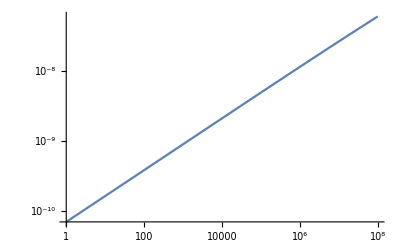

```mathematica
LogLogPlot[predrateexpanded/.{Mp->OptPredMass[M],ϵEprey->0},{M,1,10^8},PlotRange->All]
```

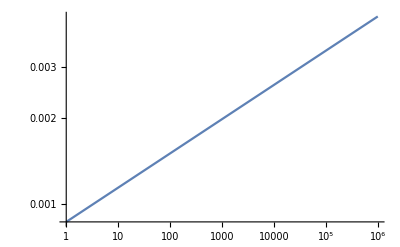

```mathematica
LogLogPlot[PredDensity[Mp],{Mp,1,10^6}]
```

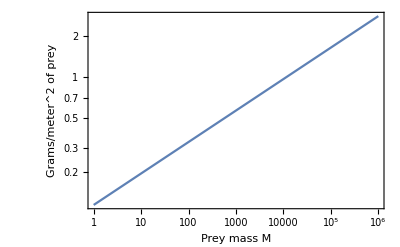

```mathematica
LogLogPlot[ (M)*(0.1156*M^-0.77),{M,1,10^6},Frame->True,FrameLabel->{"Prey mass M","Grams/meter^2 of prey"}]
```

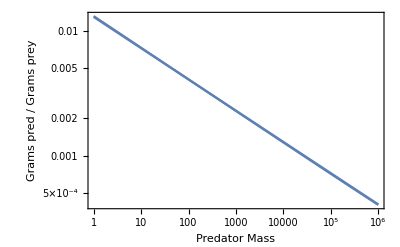

```mathematica
Show[{
LogLogPlot[Ypredexpanded/.{M->OptPreyMass[Mp],ϵEprey->0},{Mp,1,10^6},Frame->True, FrameLabel->{"Predator Mass","Grams pred / Grams prey"}] ,(*Ypred is the grams of predator / grams of prey*)
LogLogPlot[Exp[-4.35]*x^-0.25,{x,1,10^6}],
ListPlot[Table[{10^i,Ypred[10^i,OptPreyMass[10^i],0]},{i,1,6}]]
}]
```

Slopes for the elements of the predator mortality rate:

```mathematica
LinearModelFit[Log@Table[{10^i,Ypred[10^i,OptPreyMass[10^i],0]},{i,1,6,0.1}],x,x]
LinearModelFit[Log@Table[{10^i,kPredMaxGrowth[10^i]},{i,1,6,0.1}],x,x]
LinearModelFit[Log@Table[{10^i,λPred[10^i]},{i,1,6,0.1}],x,x]
LinearModelFit[Log@Table[{10^i,PredDensity[10^i]},{i,1,6,0.1}],x,x]
```

FittedModel[-4.34127-0.251827 x]

FittedModel[5.1446-0.250404 x]

FittedModel[-15.409-0.254913 x]

FittedModel[-7.05612+0.12 x]

```mathematica
-0.25+0.12-(-0.25+-0.25)
```

0.37

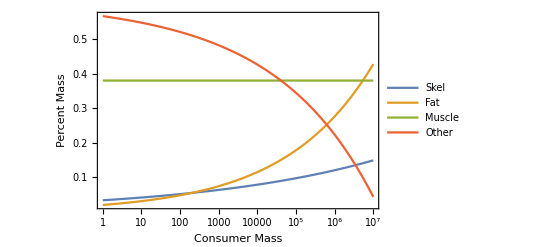

```mathematica
LogLinearPlot[{(1/M)*massSkeletalgrams[M],(1/M)*massFatgrams[M],(1/M)*massMusclegrams[M],(1/M)*massOthergrams[M]},{M,1,10^7},PlotRange->{0,All},Frame->True,FrameLabel->{"Consumer Mass","Percent Mass"},PlotLegends->{"Skel","Fat","Muscle","Other"}]
```

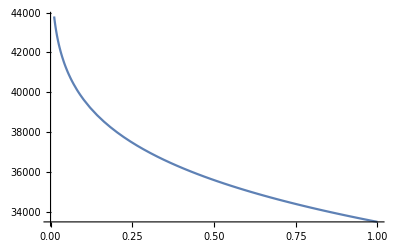

```mathematica
Plot[Eprey[M,0],{M,1,10^8}]
```

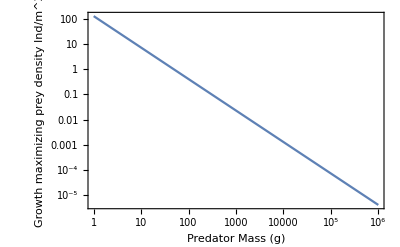

```mathematica
LogLogPlot[(1/OptPreyMass[Mp])*kPredMaxGrowth[Mp],{Mp,1,10^6},Frame->True,FrameLabel->{"Predator Mass (g)","Growth maximizing prey density Ind/m^2"},PlotRange->All]
```

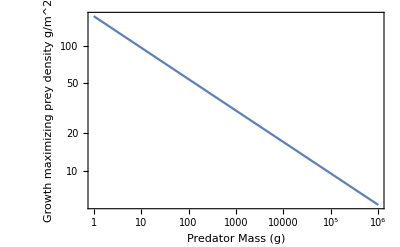

```mathematica
LogLogPlot[kPredMaxGrowth[Mp],{Mp,1,10^6},Frame->True,FrameLabel->{"Predator Mass (g)","Growth maximizing prey density g/m^2"}]
```

```mathematica
FatJperG+ProteinJperG
```

55600

```mathematica
percentconsumable[10^6]
```

0.999886

```mathematica
avgmortratePred[{q0_,α_,texp_}]:=((-1+ⅇ^(texp α)) q0)/(texp α);
```

```mathematica
avgmortratePredexpanded = avgmortrate[{a0*Mp^b0, a1*Mp^b1, a2*Mp^b2}]
```

(a0 (-1+ⅇ^(a1 a2 Mp^(b1+b2))) Mp^(b0-b1-b2))/(a1 a2)

```mathematica
λPred[Mp]- avgmortrate[{1.88*10^-8*Mp^-0.56, 1.45*10^-7*Mp^-0.27,4.04*10^6*Mp^0.30}]
```

-(3.20929×10^-8 (-1+ⅇ^(0.5858 Mp^0.03)))/Mp^0.59-(7.25474×10^-7)/(Mp^(1/4) Log[0.0127415/(1-0.558075/Mp^0.02)])

```mathematica
GrowthMortPredRatio[Mp_]:=-(3.2092864458859676*^-8 (-1+ⅇ^(0.5858 Mp^0.02999999999999997)))/Mp^0.5900000000000001-(7.254743284040163*^-7)/(Mp^(1/4) Log[0.012741455098566168/(1-0.5580754698496868/Mp^0.01999999999999999)])
```

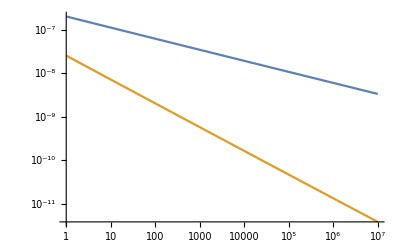

```mathematica
LogLogPlot[{λPred[Mp], avgmortrate[{1.88*10^-8*Mp^-0.56, 1.45*10^-7*Mp^-0.27,4.04*10^6*Mp^0.30}]},{Mp,1,10^7}]
```

```mathematica
Show[{
LogLinearPlot[OptPredMass[M]/OptPreyMass[M],{M,1,10^7}]
}]
```

-Graphics-